# AMS-511 Foundations of Quantitative Finance

## Fall 2018 — Assignment 04

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Question 1

Use FinancialBond[ ] to compute the following:

A newly issued $10,000 bond with a ten-year term has a 4% coupon rate and pays semi-annually. The current market yield for a ten-year bond of this type is 3.7%. What is the current market price of the bond?

```mathematica
FinancialBond[{"Coupon"->0.04,"FaceValue"->10000,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->0.037,"Settlement"->0}]
```

10248.9

A $10,000 bond with a five-year term, a 3.7% coupon rate paying semi-annually was issued eight months ago. The current market yield is 3.5%.

What is the current price of the bond?

```mathematica
FinancialBond[{"Coupon"->0.037,"FaceValue"->10000,"Maturity"->5,"CouponInterval"->1/2},{"InterestRate"->0.035,"Settlement"->8/12}]
```

10079.4

What is the accrued interest on the bond?

```mathematica
FinancialBond[{"Coupon"->0.037,"FaceValue"->10000,"Maturity"->5,"CouponInterval"->1/2},{"InterestRate"->0.035,"Settlement"->8/12}, "AccruedInterest"]
```

61.6667

Consider a $10,000 semi-annual bond with a twenty-year term and a 4.5% coupon rate. The bond was issued five-years ago and currently trades at a price of $10,500. What is the yield on the bond?

```mathematica
FindRoot[FinancialBond[{"Coupon"->0.045,"FaceValue"->10000,"Maturity"->20,"CouponInterval"->1/2},{"InterestRate"->p,"Settlement"->5}]==10500,{p,0.045}]
```

{p→0.0405191}

## Question 2

Consider two assets with mean returns, standard deviations and correlation matrix:

μ=(0.08
0.05)

σ=(0.10
0.04)

C=(1 | 0.4
0.4 | 1)

ℳ_1=min_x {1/2 x^T Σ x-λ μ^T x |  1^T x=1}

Compute the covariance matrix Σ.

```mathematica
vnMean={0.08,0.05};
vnSigma={0.1,0.04};
mnCor={{1,0.4},{0.4,1}};
mnCov=KroneckerProduct[vnSigma,vnSigma]mnCor
```

{{0.01,0.0016},{0.0016,0.0016}}

Consider the following portfolio optimization problem ℳ_1 (short positions allowed):

ℳ_1=min_x {1/2 x^T Σ x-λ μ^T x |  1^T x=1}

Compute and plot a mean-variance efficient frontier for a portfolio consisting of these two assets.

{{0.,{2.27374×10^-17,1.}},{0.01,{0.0357143,0.964286}},{0.02,{0.0714286,0.928571}},{0.03,{0.107143,0.892857}},{0.04,{0.142857,0.857143}},{0.05,{0.178571,0.821429}},{0.06,{0.214286,0.785714}},{0.07,{0.25,0.75}},{0.08,{0.285714,0.714286}},{0.09,{0.321429,0.678571}},{0.1,{0.357143,0.642857}}}

{{0.,{0.04,0.05}},{0.01,{0.0401337,0.0510714}},{0.02,{0.0405322,0.0521429}},{0.03,{0.0411877,0.0532143}},{0.04,{0.0420883,0.0542857}},{0.05,{0.0432187,0.0553571}},{0.06,{0.0445614,0.0564286}},{0.07,{0.0460977,0.0575}},{0.08,{0.0478091,0.0585714}},{0.09,{0.0496775,0.0596429}},{0.1,{0.0516859,0.0607143}}}

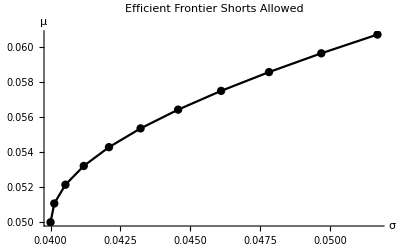

```mathematica
xOptimalPortfolio[mnCov_,vnMean_,λ_]:=Module[
{mi,v1,vμ},
mi=Inverse[mnCov];
v1=Total/@mi;
vμ=mi.vnMean;
λ vμ+((1-λ Total[vμ])/Total[v1])v1
];
xPortSdevMean[x_,{μ_,Σ_}]:={√(x.Σ.x),μ.x};
vuEfficientPortfolios=Table[
{λ,xOptimalPortfolio[mnCov,vnMean,λ]},
{λ,0.,0.1,0.01}
]
vuEfficientFrontier=Transpose[{First/@vuEfficientPortfolios,xPortSdevMean[#,{vnMean,mnCov}]&/@(Last/@vuEfficientPortfolios)}]
ListPlot[
MapThread[Tooltip,{Last/@vuEfficientFrontier,vuEfficientPortfolios}],
PlotStyle->{PointSize[Large],Black},
PlotLabel->Style["Efficient Frontier Shorts Allowed",FontSize->14],
Joined->True,Mesh->All,
AxesLabel->{"σ","μ"}
]
```

If the risk-free rate r_f=0.01, what is the tangent portfolio?

```mathematica
xTangentPortfolio[mnCov_,vnMean_,nRiskFree_]:=#/Total[#]&[Inverse[mnCov].(vnMean-nRiskFree)];
vnTangentPortfolio=xTangentPortfolio[mnCov, vnMean, 0.01]
xPortSdevMean[vnTangentPortfolio, {vnMean, mnCov}]
```

{0.142857,0.857143}

{0.0420883,0.0542857}

Consider the following portfolio optimization problem ℳ_2 (no short positions allowed):

ℳ_2=min_x {1/2 x^T Σ x-λ μ^T x |  1^T x=1∧x_i≥0}

Compute and plot a mean-variance efficient frontier for a portfolio consisting of these two assets.

{{0.,{1.47094×10^-8,1.}},{0.01,{0.0357143,0.964286}},{0.02,{0.0714289,0.928571}},{0.03,{0.107143,0.892857}},{0.04,{0.142857,0.857143}},{0.05,{0.178571,0.821429}},{0.06,{0.214286,0.785714}},{0.07,{0.25,0.75}},{0.08,{0.285714,0.714286}},{0.09,{0.321429,0.678571}},{0.1,{0.357143,0.642857}}}

{{0.,{0.04,0.05}},{0.01,{0.0401337,0.0510714}},{0.02,{0.0405322,0.0521429}},{0.03,{0.0411877,0.0532143}},{0.04,{0.0420883,0.0542857}},{0.05,{0.0432187,0.0553571}},{0.06,{0.0445614,0.0564286}},{0.07,{0.0460977,0.0575}},{0.08,{0.0478091,0.0585714}},{0.09,{0.0496775,0.0596429}},{0.1,{0.0516859,0.0607143}}}

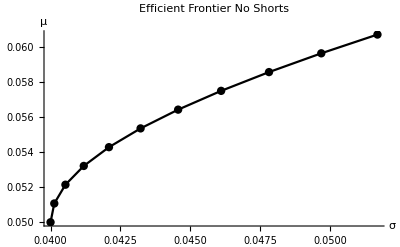

```mathematica
x={x1,x2};
xEfficientPortfolioNoShorts[λ_,{vnMean_,mnCov_}]:=x/.Last[NMinimize[{(x.mnCov.x)/2-λ vnMean.x,And@@Join[{Total[x]==1},#≥0&/@x]},x]];
vuEfficientPortfoliosNoShorts=Table[
{λ,xEfficientPortfolioNoShorts[λ,{vnMean,mnCov}]},
{λ,0.,0.1,0.01}
]
vuEfficientFrontier=Transpose[{First/@vuEfficientPortfoliosNoShort,xPortSdevMean[#,{vnMean,mnCov}]&/@(Last/@vuEfficientPortfoliosNoShort)}]
ListPlot[
MapThread[Tooltip,{Last/@vuEfficientFrontier,vuEfficientPortfoliosNoShort}],
PlotStyle->{PointSize[Large],Black},
PlotLabel->Style["Efficient Frontier No Shorts",FontSize->14],
Joined->True,Mesh->All,
AxesLabel->{"σ","μ"}
]
```

Compare the efficient frontiers of ℳ_1 and ℳ_2.

ℳ_1 and ℳ_2 have the same efficient frontiers. ℳ_1 allows negative positions but its efficient frontier consists of all positive positions. So, restricting the solutions to positive will have no effect on the efficient frontier of ℳ_2.

## Question 3

Use FinancialData[ ] to download the data required to complete the following:

Secure the closing price data for Microsoft and Apple so far for 2018 (i.e., through 2018-09-18).

```mathematica
vdnMSFTClose=FinancialData["MSFT","Close",{2018,1,1}];
vdnAAPLClose=FinancialData["AAPL","Close",{2018,1,1}];
```

Plot the closing price of Microsoft and Apple on the same graph.

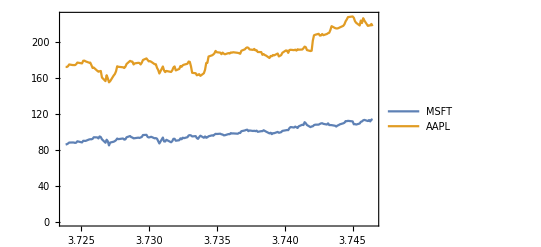

```mathematica
DateListPlot[{vdnMSFTClose, vdnAAPLClose},PlotLegends->{"MSFT","AAPL"}]
```

Compute or download the daily returns for Microsoft and Apple and plot them on separate graphs.

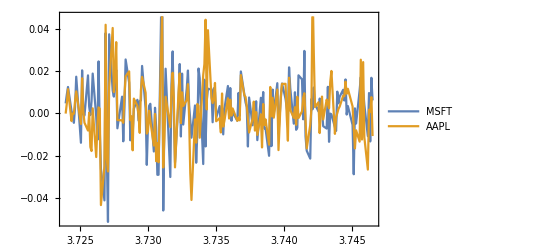

```mathematica
vdnMSFTReturns=FinancialData["MSFT","Return",{2018,1,1}];
vdnAAPLReturns=FinancialData["AAPL","Return",{2018,1,1}];
DateListPlot[{vdnMSFTReturns, vdnAAPLReturns},PlotLegends->{"MSFT","AAPL"}]
```

Generate a table which contains for each stock in the Dow Jones Industrial index: the ticker symbol, name, and market capitalization.

```mathematica
vsDjiTickers=FinancialData["^DJI","Members"];
vsDjiNames=FinancialData[vsDjiTickers,"Name"];
vnDjiMarketCaps=FinancialData[vsDjiNames,"MarketCap"];
TableForm[
{vsDjiTickers,vsDjiNames,vnDjiMarketCaps}ᵀ,
TableHeadings->{Automatic,{"Ticker","Name","MarketCap"}}
]
```

| Ticker | Name | MarketCap
1 | NYSE:MMM | 3M | 1.28433×10^11
2 | NYSE:AXP | American Express | 9.54142×10^10
3 | NASDAQ:AAPL | Apple | 1.06983×10^12
4 | NYSE:BA | Boeing | 2.16854×10^11
5 | NYSE:CAT | Caterpillar | 9.35074×10^10
6 | NYSE:CVX | Chevron | 2.31475×10^11
7 | NASDAQ:CSCO | Cisco | 2.33939×10^11
8 | NYSE:KO | Coca-Cola | 1.9821×10^11
9 | NYSE:DIS | Disney | 1.66006×10^11
10 | NYSE:DWDP | DowDuPont Inc | 1.62095×10^11
11 | NYSE:XOM | Exxon Mobil | 3.6061×10^11
12 | NYSE:GS | Goldman Sachs | 9.12178×10^10
13 | NYSE:HD | Home Depot | 2.44826×10^11
14 | NASDAQ:INTC | Intel | 2.17436×10^11
15 | NYSE:IBM | IBM | 1.38935×10^11
16 | NYSE:JNJ | Johnson & Johnson | 3.83226×10^11
17 | NYSE:JPM | JPMorgan Chase | 4.01253×10^11
18 | NYSE:MCD | McDonald's | 1.2994×10^11
19 | NYSE:MRK | Merck & Co. | 1.91452×10^11
20 | NASDAQ:MSFT | Microsoft | 8.77882×10^11
21 | NYSE:NKE | Nike | 1.37886×10^11
22 | NYSE:PFE | Pfizer | 2.62095×10^11
23 | NYSE:PG | Procter & Gamble | 2.15803×10^11
24 | NYSE:TRV | Travelers | 3.63339×10^10
25 | NYSE:UNH | UnitedHealth | 2.5629×10^11
26 | NYSE:UTX | United Technologies | 1.13672×10^11
27 | NYSE:VZ | Verizon Communications | 2.24858×10^11
28 | NYSE:V | Visa | 3.46226×10^11
29 | NASDAQ:WBA | Walgreens Boots Alliance Inc | 7.23916×10^10
30 | NYSE:WMT | Wal-Mart Stores | 2.83143×10^11